# Billiards in a Cusp

## Function Definitions

```mathematica
$Assumptions = 0 <=t<=Pi/2;
```

```mathematica
GetUnitTangent[f_, dom_, pt_] :=Normalize[N[Flatten[D[f,t]/.NSolve[f[[1]] == pt[[1]] && t ∈ dom ,t]]]];
```

```mathematica
(* Reflect vector v over the UNIT VECTOR u *)
ReflectVec[v_, u_] := 2(Dot[v,u])u - v;
```

```mathematica
(* finds intersection of curve param. by f and the RAY generated by v *)
(* f is required to be parametrized by t *)
FindIntersection[f_, dom_, v_, pt_] := Flatten[
(pt + v s)/.If[
Length[#]==0,
{s->10},
#]&@
Flatten[MinimalBy[ 
NSolve[
pt[[1]] + v[[1]] s == f[[1]] && pt[[2]] + v[[2]] s == f[[2]] && s>=0 && t ∈ dom, 
{t, s}
],
t/.# &]
]
];
```

```mathematica
NextPt[pt_,v_] := ({#, ReflectVec[v,GetUnitTangent[c,Interval[{cdom[[2]],cdom[[3]]}], #]]}&@FindIntersection[c, Interval[{cdom[[2]], cdom[[3]]}], v, pt]);
```

## Unit Tests

These only need to be run if you change function definitions above.

### Unit Tangents

```mathematica
cases = {

{ 
{Cos[t], Sin[t]},
Interval[{0,2Pi}],
Table[
{ 
{Cos[t], Sin[t]},
{-Sin[t],Cos[t]} 
},
{t, 0, 2Pi, 2Pi/10}
]
},

{
{t-Sin[t], 1-Cos[t]},
Interval[{0, 2Pi}],
Table[
{ 
{t-Sin[t], 1-Cos[t]},
{1-Cos[t], Sin[t]} 
},
{t, 0, 2Pi, 2Pi/10}
]
}

};

res[case_] := Map[
GetUnitTangent[case[[1]],case[[2]],First[#] ]  == Last[#]&, case[[3]]
];

Map[If[ And@@res[#],Print["Pass"],Print["Fail"]] &, cases];
```

Pass

Pass

### Find Intersection

```mathematica
cases = {

{ 
{t, 3},
Reals,
{1,2},
{0,0},
{3/2,3}
},

{
{Cos[t], Sin[t]},
Interval[{0,2Pi}],
{0,1},
{1/2,0},
{Cos[Pi/3],Sin[Pi/3]}
}

};

res[case_] := FindIntersection[case[[1]],case[[2]], case[[3]] , case[[4]]] == case[[5]];
Map[If[ res[#],Print["Pass"],Print["Fail"]] &, cases];
```

Pass

Pass

## Simulation

### Define Two Curves and Initial Conditions

```mathematica
f = {-t, t^2};
fdom ={t,0,.75};
```

```mathematica
g = {-Sin[t], Cos[t]}+{0,1};
gdom = {t, Pi/4, Pi};
```

```mathematica
initpt = f/.{t->.5};
initv = {0,-1};
n=10;
```

### Run Simulation

```mathematica
pts = { {initpt, initv} };
Dynamic[i]
c = g;
cdom = gdom;
For[ i = 1, i <n, i = i +1, 
AppendTo[pts, NextPt@@Last[pts]]; 
If[ 
TrueQ[c == g], 
(c = f; cdom = fdom),
(c = g; cdom=gdom)
]
]
```

Dot::dotsh: Tensors {-0.968655,0.24841} and {-0.433037,-0.558998,0.433037,-0.558998} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {-0.866074 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},-1.118 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},0.866074 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},-1.118 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998}}+{0.968655,-0.24841} cannot be combined.

```mathematica
pts//FullSimplify
```

{{{-0.5,0.25},{0,-1}},{{-0.5,0.133975},{0.866025,0.5}},{{-0.42265,0.178633},{-0.348828,-0.937187}},{{-0.44943,0.106684},{0.544618,0.838684}},{{-0.409705,0.167858},{-0.71526,-0.698858}},{{-0.464429,0.114389},{0.168179,0.985756}},{{-0.449476,0.202029},{-0.962342,-0.271842}},{{-0.55927,0.171015},{-0.108267,0.994122}},{{-0.57689,0.332802},{-0.968655,0.24841}},{{-0.790543,0.387593},{0.968655,-0.24841}+{-0.866074 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},-1.118 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},0.866074 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998},-1.118 {-0.968655,0.24841}.{-0.433037,-0.558998,0.433037,-0.558998}}}}

### Generate Plots

```mathematica
bg = Show[
{
Apply[ParametricPlot[#1,  #2] & , {f, fdom}], 
Apply[ParametricPlot[#1,  #2] & ,{g, gdom}]
},
PlotRange->{ {-1,0}, {0,.6}}
];
```

```mathematica
ϵ = .05;
eplg = Map[ #[[1]] &, pts];
(*Join[*) 
{Red, Thick, Line[eplg]};
(*, Table[ 
If[
EvenQ[n],
{Green,Thin,Line[{{ 0, 0}, eplg[[n]]}], Line[{eplg[[n]], (1+ϵ) eplg[[n]]}]},
{Magenta,Thin,Line[{ { 0, 3/2}, eplg[[n]]}], Line[{eplg[[n]], eplg[[n]] + 2 ϵ(eplg[[n]]-{ 0, 3/2})}]}
],
{n, 1, Length[eplg]}
]*)
(*];*)
plt = Show[bg, Graphics[%]];
```

### Plots

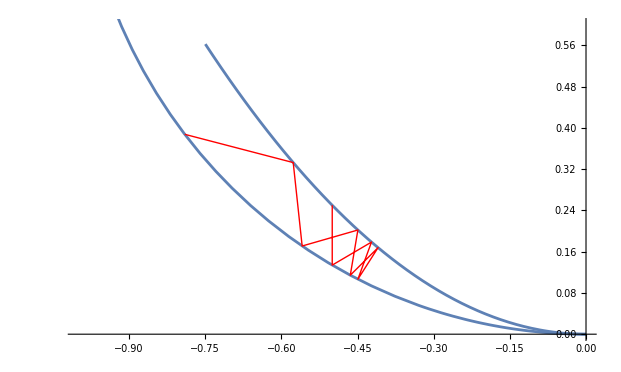

```mathematica
plt
```